# Loading Initial Data

The results were exported from the simulation application as multiple 2D arrays of entries, each entry is 5 parameters in double precision format:
	• Lobe θ
	• Lobe roughness α
	• Lobe Scale σ
	• Lobe non-uniform Scale σ_n (also called “flattening factor”)
	• Lobe masking importance m

Each 2D array corresponds to a different albedo, there are currently 4 surface albedos that were simulated: 1, 0.75, 0.5 and 0.25
We’re currently focusing on 2nd order scattering since models for 1st order scattering are quite well documented already.

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]](* So Mathematica knows the directory for our files *)
resX = 20; (* Incoming direction in [0,π/2[ *)
resY=10; (* Roughness in [0,1] *)
resZ=8;  (* Albedos in [0,1[ *)
rawFiles = Table[{i},{i,1,resZ}];
For[albedo=0,albedo<resZ,albedo++,{
str=OpenRead["results_order3_slice" <> ToString[albedo] <> ".bin",{BinaryFormat->True}];
rawFile = BinaryReadList[str,{"Real64","Real64","Real64","Real64","Real64"}];
rawFiles[[1+albedo]]= Table[Table[  rawFile[[1+resX*(j-1)+(i-1)]], {i,1,resX}],{j,1,resY}];
Close[str];
} ]
MatrixForm[rawFiles];
rawFiles[[1]];
```

D:\Workspaces\GodComplex\Tools\TestMSBSDF\Results\Diffuse2\3) Fitting Other Orders\Export

```mathematica
paramsScale = Table[Table[rawFiles[[albedo]][[j]][[i]][[3]],{j,1,resY},{i,1,resX}], {albedo,1,resZ}];
MatrixForm[ paramsScale[[1]] ];
MatrixForm[ paramsScale[[2]] ];
MatrixForm[ paramsScale[[3]] ];

Show[
Table[ ListPlot3D[paramsScale[[albedo]],PlotRange->{0,0.4},PlotStyle->GrayLevel[1-(albedo-1)/resZ],AxesLabel->{"α","8 albedos\n(simulated for θ=0 using the analytical diffuse\nlobe model with only the scale as a free parameter)"}],
{ albedo, 1, resZ }]
]
```

-Graphics3D-

Here is the representation of the scale parameter for order 2, we notice it’s very similar so we’ll attempt to fit the same model, only with an amplitude change...

## Re-Using and fitting the order 2 model

So we end up with 4 coefficients a, b, c and d depending on surface roughness α_s to form an order 3 polynomial depending on μ = cos(θ) :

	a(α_s)= 0.0288133-0.921537 α+6.63273 α^2-4.5957 α^3
	b(α_s)= -0.0966326+7.21414 α-19.7868 α^2+11.0421 α^3
	c(α_s)= 0.109357-10.7904 α+28.508 α^2-15.6653 α^3
	d(α_s)=-0.0437643+5.2492 α-13.5827 α^2+7.34841 α^3
	
	σ(μ,α_s) =a(α_s) + b(α_s)μ + c(α_s) μ^2 + d(α_s) μ^3

```mathematica
Clear[a,b,c,d,σ,μ,fA,fB,fC,fD]
fA[α_]=0.028813261153483097-0.9215374811620882 α+6.632726114385572 α^2-4.5957022306534 α^3
fB[α_]= -0.09663259042197028+7.214143602200921 α-19.786845117100626 α^2+11.042058883797509 α^3
fC[α_]= 0.10935692546815767-10.790405157520944 α+28.50803667636733 α^2-15.665258273262731 α^3
fD[α_]=-0.04376425480146207+5.2491960091879 α-13.582707339717146 α^2+7.348408854602616 α^3
fScale[μ_,α_] =fA[α] + fB[α]μ + fC[α] μ^2 + fD[α] μ^3 ;
Plot[fA[α],{α,0,1}];
Plot[fB[α],{α,0,1}];
Plot[fC[α],{α,0,1}];
Plot[fD[α],{α,0,1}];
Plot3D[fScale[μ,α],{μ,0,1},{α,0,1},AxesLabel->{"cos(θ)","α_s""α"},PlotLabel->"Lobe Scale factor",PlotRange->{0,1.3}]
```

(0.109357-10.7904 α+28.508 α^2-15.6653 α^3) (0.0288133-0.921537 α+6.63273 α^2-4.5957 α^3) (-0.0437643+5.2492 α-13.5827 α^2+7.34841 α^3) (-0.0966326+7.21414 α-19.7868 α^2+11.0421 α^3)

-Graphics3D-

### Finding the matching amplitudes

```mathematica
paramsScaleMuAlpha = Table[
	Table[
		{ Cos[Mod[i,resX]/resX*π/2], 1-Quotient[i,resX]/(resY-1),paramsScale[[albedo]][[1+Quotient[i,resX]]][[1+Mod[i,resX]]]},{i,0,resX*resY-1}]
, {albedo,1,resZ}];

paramsScaleMuAlpha[[1]];
Show[Table[ListPlot3D[paramsScaleMuAlpha[[albedo]]],{albedo,1,resZ}]]
```

-Graphics3D-

{{amp→0.363902},{amp→0.24313},{amp→0.153473},{amp→0.087976},{amp→0.0452926},{amp→0.0181574},{amp→0.00405192},{amp→1.44633×10^-6}}

{{1,0.363902},{7/8,0.24313},{3/4,0.153473},{5/8,0.087976},{1/2,0.0452926},{3/8,0.0181574},{1/4,0.00405192},{1/8,1.44633×10^-6}}

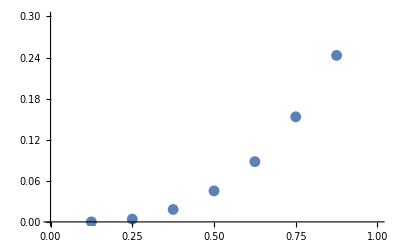

```mathematica
modelRho=amp * fScale[μ,α];
fittingRho = Table[FindFit[ paramsScaleMuAlpha[[albedo]],{modelRho},{amp},{μ,α} ],{albedo,1,resZ}]
listAmps=Table[{1-(albedo-1)/resZ, amp/.fittingRho[[albedo]]},{albedo,1,resZ}];
ListPlot[listAmps,PlotRange->{0,0.3}]
```

{amp→0.363902}

0.363902

{a→-0.000576999,b→-0.00439469,c→0.0109666,d→0.357697}

-0.000576999-0.00439469 ρ+0.0109666 ρ^2+0.357697 ρ^3

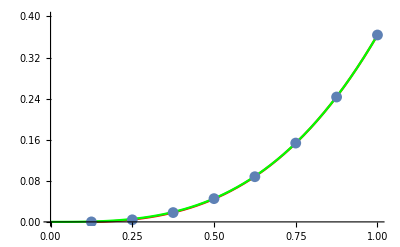

```mathematica
fittingRho[[1]]
maxAmp = Evaluate[amp/.fittingRho[[1]]]
modelAmp=a+b*u+c*u^2+d*u^3;
fittingAmp=FindFit[listAmps,modelAmp,{a,b,c,d},u]
fAmp[ρ_]=Evaluate[modelAmp/.fittingAmp/.u->ρ]
fAmp2[ρ_]=maxAmp * ρ^3;
Show[
Plot[fAmp[ρ],{ρ,0,1},PlotStyle->Red,PlotRange->{0,0.4}],
Plot[fAmp2[ρ],{ρ,0,1},PlotStyle->Green,PlotRange->{0,0.4}],
ListPlot[listAmps]
]
```

Final Expression

We can now obtain the final expression for the function matching the lobe scale factor at order 3:

σ_3(μ,α, ρ) = ρ^3 [0.363902 * σ_2(μ,α)]

```mathematica
fScale3[ μ_,α_,ρ_] = ρ^3 * (0.363902052363025*fScale[μ,α]);
Show[Table[Plot3D[fScale3[μ,α,1-albedo/resZ],{μ,0,1},{α,0,1},AxesLabel->{"θ","α","lobe scale"},PlotStyle->GrayLevel[1-albedo/resZ]],{albedo,0,resZ}]]
```

-Graphics3D-

#### Checking our Matching

We can’t expect an exact match because we took the liberty to re-use the scale expression from order 2 to match the scale of order 3, which is slightly different, but we get very close anyway...

```mathematica
Show[ 
Table[ListPlot3D[paramsScaleMuAlpha[[albedo]],{ PlotRange->{0,0.4},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->GrayLevel[1-(albedo-1)/resZ]],{albedo,1,6}],
Table[Plot3D[fScale3[μ,α,1-(albedo-1)/resZ],{μ,0,1},{α,0,1},{ PlotRange->{0,1.2},AxesLabel->{"θ","α_s","scale σ for various albedos"}},PlotStyle->Red],{albedo,1,6}]
]
```

-Graphics3D-